```mathematica
raw = Import["/Users/rithika/utkcms/mu-cooling/channels/finescan-single-coil/output/xoffset20-z-pz.csv"];
```

```mathematica
Dimensions[raw]
```

{3025,2}

```mathematica
z = raw[[All, 1]];
```

```mathematica
Dimensions[z]
```

{3024}

```mathematica
pz = raw[[All, 2]];
```

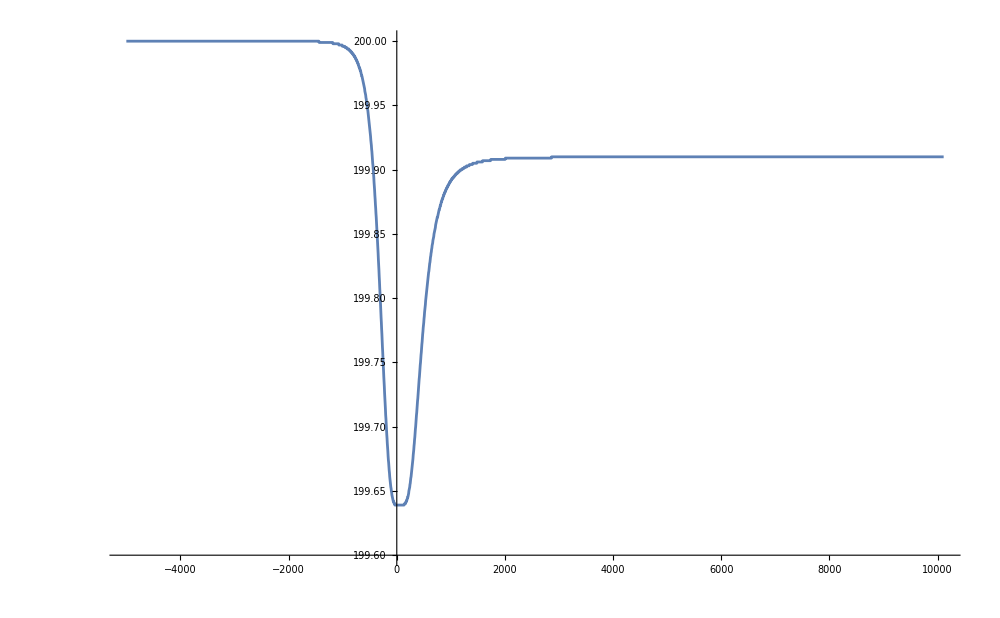

```mathematica
plot = ListLinePlot[raw[[All, {1, 2}]], ImageSize->1000, PlotRange->{All, {199.6, 200}}, PlotStyle-> Thickness[0.002]]
```

```mathematica
Export["/Users/rithika/utkcms/mu-cooling/plots/mathematica-pz-vs-z-xoffset20.png", plot]
```

/Users/rithika/utkcms/mu-cooling/plots/mathematica-pz-vs-z-xoffset20.png